```mathematica
(* bonding curve p(s) = c*s^k+p_0 *)
p[s_]=s^k+p0 /.{p0->0,k->4}
```

s^4

```mathematica
(* The ratio of price outside AMM *)
```

```mathematica
p[y]/p[x]
```

```mathematica
y^4/x^4
(*we use the dy/dx = -p[y]/p[x] as the no arbitrage conditions then *)
```

```mathematica
solution = DSolve[y'[x]== -(p[y[x]])/(p[x]),y[x],x]
```

{{y[x]→x/((-1-3 x^3 C[1])^(1/3))},{y[x]→-((-1)^(1/3) x)/((-1-3 x^3 C[1])^(1/3))},{y[x]→((-1)^(2/3) x)/((-1-3 x^3 C[1])^(1/3))}}

```mathematica
g[x_]=y[x]/.solution
```

```mathematica
{x/((-1-3 x^3 C[1])^(1/3)),-((-1)^(1/3) x)/((-1-3 x^3 C[1])^(1/3)),((-1)^(2/3) x)/((-1-3 x^3 C[1])^(1/3))}
```

```mathematica
(*we get a lot of solutions, and set c1 as some values*)
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {m[x]→((-1+k) (x^Plus[«2»]/Plus[«2»]-1))^(1/(1-k))}.

```mathematica
t[x_] = Table[g[x][[1]]/.C[1]->j,{j,-5,-1}]
```

{x/((-1+15 x^3)^(1/3)),x/((-1+12 x^3)^(1/3)),x/((-1+9 x^3)^(1/3)),x/((-1+6 x^3)^(1/3)),x/((-1+3 x^3)^(1/3))}

```mathematica
(* the relationship between y, which is the supplement of token A, and x, which is the supplement of token B, as follows, the convexity is far more than the usual one*)
```

```mathematica
Plot[t[x],{x,0,2}]
```

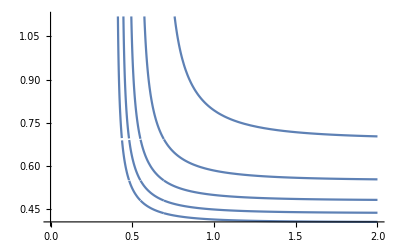

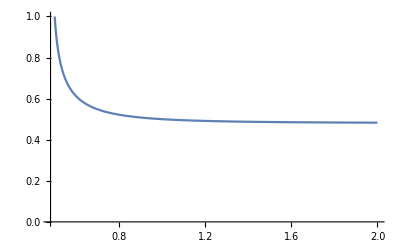

```mathematica
(* we just try x/((-1+9 x^3)^(1/3)) as example*)
Plot[x/((-1+9 x^3)^(1/3)),{x,0,2},PlotRange->{0,1}]
```

```mathematica
(*so the maxvalue the liquidity providers want to get is p[x]*x+p[y]*y,then what he need to do is little by little pump the price of A and B to the maxvalue
and ensure there's no arbitrage so that the shock cost will be zero, which means we must follow the curve to pump the price, the integration of the value is the max profit*)

MaxValue[x/((-1+9 x^3)^(1/3))*p[x/((-1+9 x^3)^(1/3))] +x*p[x],x]
```

∞

```mathematica
(* however, under the p(s) = 1*s^4+0 conditions, the maxvalue is infinity, which means the more token x or the more token y, the higher the max value. Then the max profit is infinity. Only if the fees are less than the profit. If the fees are Infinity too, then the profit will be -Infinity. *)

(* try other case*)
(* bonding curve p(s) = c*s^k+p0  *)*)
```

```mathematica
q[s_]=c*s^k+p0 /.{p0->1,k->1,c->-1}
```

1-s

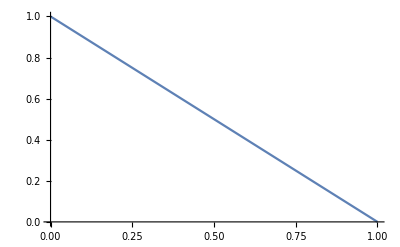

```mathematica
1-s
Plot[q[s],{s,0,1}]
```

```mathematica
q[y]/q[x]
```

(1-y)/(1-x)

```mathematica
solution2 = DSolve[y'[x]== -(q[y[x]])/(q[x]),y[x],x]
```

{{y[x]→-x/(1-x)+C[1]/(1-x)}}

```mathematica
h[x_]=y[x]/.solution2
```

{-x/(1-x)+C[1]/(1-x)}

```mathematica
t[x_] = Table[h[x][[1]]/.C[1]->j,{j,1,5}]
```

{1/(1-x)-x/(1-x),2/(1-x)-x/(1-x),3/(1-x)-x/(1-x),4/(1-x)-x/(1-x),5/(1-x)-x/(1-x)}

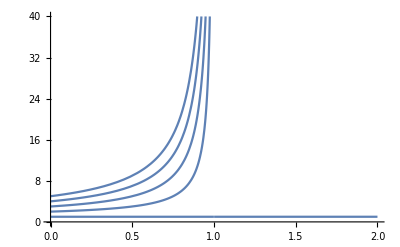

```mathematica
Plot[t[x],{x,0,2},PlotRange->{0,40}]
```

```mathematica
(* we just set 1/(1-x)-x/(1-x) as example，so we get the maxvalue*)
MaxValue[(1/(1-x)-x/(1-x))*q[1/(1-x)-x/(1-x)] +x*q[x],x]
```

1/4

```mathematica
ArgMax[(1/(1-x)-x/(1-x))*q[1/(1-x)-x/(1-x)] +x*q[x],x]
```

1/2

```mathematica
h[1/2]/.C[1]->1
```

{1}

```mathematica
(* then we just need to exchange token x for token y or token y for token x to get the x=1/2,y=1 result, for there is no arbitrage, we do not need to invest more into it. If there's arbitrage, we need to cover the loss of the arbitrage, which is the shock loss. *)
(* The last question is if there's fee in it, which is the cost, what it is:*)
fee = (x0-xdestination)*f
```

f (x0-xdestination)

```mathematica
(* try other case,which is the most usual case,(* bonding curve p(s) = c1*s^2+c2*s+p0 *)*)
o[s_]=c1*s^2+c2*s+p0 /.{p0->0,c1->-1,c2->2}
```

2 s-s^2

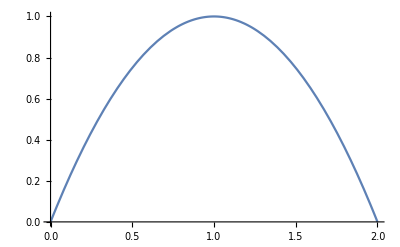

```mathematica
Plot[o[s],{s,0,2}]
```

o[y]/o[x]

(2 y-y^2)/(2 x-x^2)

```mathematica
solution3 = DSolve[y'[x]== -(o[y[x]])/(o[x]),y[x],x]
```

{{y[x]→-(2 (-2+x))/(2-x+ⅇ^(2 C[1]) x)}}

```mathematica
l[x_]=y[x]/.solution3
```

{-(2 (-2+x))/(2-x+ⅇ^(2 C[1]) x)}

```mathematica
.08
```

```mathematica
t[x_] = Table[l[x][[1]]/.C[1]->j,{j,1,5}]
```

{-(2 (-2+x))/(2-x+ⅇ^2 x),-(2 (-2+x))/(2-x+ⅇ^4 x),-(2 (-2+x))/(2-x+ⅇ^6 x),-(2 (-2+x))/(2-x+ⅇ^8 x),-(2 (-2+x))/(2-x+ⅇ^10 x)}

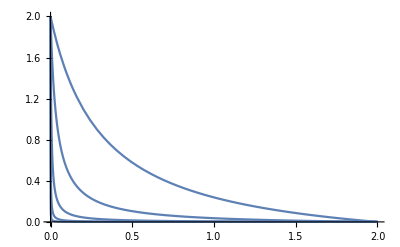

```mathematica
Plot[t[x],{x,0,2},PlotRange->{0,2}]
```

```mathematica
(* so convexity*)
```

```mathematica
MaxValue[{((2 (-2+x))/(2-x+ⅇ^-4 x))*o[(2 (-2+x))/(2-x+ⅇ^-4 x)] +x*o[x],0<x<2},x]
```

(-128 ⅇ^12-32 ⅇ^8 Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148+192 ⅇ^12 Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148+32 ⅇ^8 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^2-112 ⅇ^12 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^2-32 ⅇ^8 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^3+48 ⅇ^12 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^3-12 ⅇ^4 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^4+36 ⅇ^8 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^4-24 ⅇ^12 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^4-2 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^5+12 ⅇ^4 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^5-18 ⅇ^8 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^5+8 ⅇ^12 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^5+(Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^6-3 ⅇ^4 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^6+3 ⅇ^8 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^6-ⅇ^12 (Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^6)/(-2 ⅇ^4-Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148+ⅇ^4 Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148)^3

```mathematica
N[%198]
```

16.3075

```mathematica
ArgMax[{((2 (-2+x))/(2-x+ⅇ^-4 x))*o[(2 (-2+x))/(2-x+ⅇ^-4 x)] +x*o[x],0<x<2},x]
```

Root0.907Root[{320 ⅇ^12+(64 ⅇ^8-320 ⅇ^12-64 ⅇ^16) #1+(-32 ⅇ^8-48 ⅇ^12+176 ⅇ^16) #1^2+(-96 ⅇ^8+288 ⅇ^12-192 ⅇ^16) #1^3+(-32 ⅇ^4+168 ⅇ^8-240 ⅇ^12+104 ⅇ^16) #1^4+(-4+40 ⅇ^4-96 ⅇ^8+88 ⅇ^12-28 ⅇ^16) #1^5+(3-12 ⅇ^4+18 ⅇ^8-12 ⅇ^12+3 ⅇ^16) #1^6&,0.90651664483931}]0.9065166448393148

```mathematica
N[%197]
```

0.906517

```mathematica
Arg
```

```mathematica
o[0.907]
```

0.991351

```mathematica
(* we can still calculate the fee. For the real situation, there's arbitrage over time and the prices and exchange rates volatile over time. So in the paper he used expectation notations. In our ideal situation, no expectations are needed.*)
```